# 3-RRS: Inverse Kinematics

Convensions:
lcr - crank length;
lst - strut length;
rb - base radius;
ra - top platform radius;
{θ1, θ2, θ3} - active variables;
{ϕ1, ϕ2, ϕ3} - passive variables;
p1, p2, p3 are the three corners of the top triangle;
b1, b2, b3 are the three base points
pc is the centre of the top platform

```mathematica
solveRRdyad[{x1_, y1_}, {x2_, y2_},l1_, l2_, θ1_,θ2_] := 
Module[{a, b, c, solθ2, solθ1, solθ},
(* find the solutions for θ2 first *)
a = 2*l2*(-x1+x2); 
b = 2*l2*(-y1+y2); 
c = -l1^2+l2^2+(x1-x2)^2+(y1-y2)^2; 
solθ2 = solveLinTrig1[a, b, c, θ2];
solθ1 = {θ1->ArcTan[(-x1+x2+l2*Cos[θ2])/l1,(-y1+y2+l2*Sin[θ2])/l1]}; 
solθ = Union[solθ1/.#, #]& /@ solθ2;
(* find solution for θ1 in terms of θ2 *)
Return[solθ];
];
```

```mathematica
solveLinTrig1[a_, b_, c_, θ_] := 
Module[{Δ, sqrtΔ, onebydenominator, t, solt},
Δ =  a^2 + b^2 - c^2;
(* if Δ is available as a number, check if it is positive 
If[NumericQ[Δ], 
If[N[Δ] < 0, 
Print["solveLinTrig1::warning: the given coefficients do not lead to real values of ", θ];
];
];
*)
sqrtΔ = Sqrt[Δ];
onebydenominator = 1/(a - c); 
(* TODO: add check for the vanishing denominator following the above example *)
solt = {{t-> (b- sqrtΔ)* onebydenominator}, 
 {t-> (b+  sqrtΔ)* onebydenominator}};
Return[{θ-> ArcTan[1-t^2, 2*t]}/.solt];
];
```

```mathematica
solveRRdyad[{0,0},{1,1},0.4,1.4,θ,ϕ]//N
```

{{θ→-0.607688,ϕ→-2.07113},{θ→2.17848,ϕ→-2.64125}}

```mathematica
kϕ = {c1 -> Cos[α]Tan[ϕ/2], c2-> Sin[α]Tan[ϕ/2]};(*Not used!!*)
(*rotation matrix, Rodrigue's parameters*)
Rc[c1_,c2_,c3_]:= (1/(1+c1^2+c2^2+c3^2))*{{c1^2-c2^2-c3^2+1,2*c1*c2-2*c3,2(c2+c1*c3)},{2(c1*c2+c3),1-c1^2+c2^2-c3^2,-2*(c1-c2*c3)},{2*(c1*c3-c2),2*(c1+c2*c3),1-c1^2-c2^2+c3^2}};
(*Rotation matrix, Tait-Brian convension *)
Rtb[α_,β_,γ_]:= RotationMatrix[α,{1,0,0}].RotationMatrix[β,{0,1,0}].RotationMatrix[γ,{0,0,1}];
(*Rotation about z axis*)
Rz[θ_]:= RotationMatrix[θ,{0,0,1}];
```

```mathematica
(*centre of top platform*)
pc={x,y,z};
(*corner points of the top platform*)
p1a= pc +Rtb[α,β,γ].{ra,0,0};
p2a= pc +Rtb[α,β,γ].Rz[2π/3].{ra,0,0};
p3a= pc +Rtb[α,β,γ].Rz[4π/3].{ra,0,0};
(*solving for x,y and c3 from planarity condition*)
solxyc3=Simplify[Solve[{p1a[[2]],(Rz[-2π/3].p2a)[[2]],(Rz[-4π/3].p3a)[[2]], Cos[γ]^2+Sin[γ]^2-1}==0,{x,y,Cos[γ],Sin[γ]}]][[2]];
```

```mathematica
solxyc3
```

{x→((c1^2-c2^2) ra)/(1+c1^2+c2^2),y→-(2 c1 c2 ra)/(1+c1^2+c2^2),c3→0}

```mathematica
p1b= p1a/.solxyc3//Simplify;
p2b= Rz[-2π/3].p2a/.solxyc3//Simplify ;
p3b= Rz[-4π/3].p3a/.solxyc3//Simplify ;
```

### Spherical joint wedge vectors wrt base frame

```mathematica
(* del0 wedge angle of the spherical joint
Rotation about -y axis in each plane
*)
```

```mathematica
v1={-Sin[del0],0,Cos[del0]};
v2=Rz[2π/3].v1;
v3=Rz[4π/3].v1;
dc1=(Rtb[α,β,γ].v1/.solxyc3);
dc2=(Rtb[α,β,γ].v2/.solxyc3);
dc3=(Rtb[α,β,γ].v3/.solxyc3);
```

```mathematica
CForm[dc3[[3]]]/.{α->alpha, β->beta,Cos->cos,Sin->sin}
```

cos(alpha)*cos(beta)*cos(del0) + ((-((cos(alpha)*(cos(alpha) + cos(beta))*sin(beta))/
           Sqrt(Power(1 + cos(alpha)*cos(beta),2))) - 
        (Power(sin(alpha),2)*sin(beta))/Sqrt(Power(1 + cos(alpha)*cos(beta),2)))*sin(del0))/2.\
    + (Sqrt(3)*(((cos(alpha) + cos(beta))*sin(alpha))/
         Sqrt(Power(1 + cos(alpha)*cos(beta),2)) - 
        (cos(alpha)*sin(alpha)*Power(sin(beta),2))/Sqrt(Power(1 + cos(alpha)*cos(beta),2)))*
      sin(del0))/2.

### Passive angles ϕ for comparison with wedge angle

```mathematica
a1={Cos[gam],0,Sin[gam]}
a2=Rz[2π/3].a1
a3 = Rz[4π/3].a1
```

{Cos[gam],0,Sin[gam]}

{-Cos[gam]/2,1/2 √3 Cos[gam],Sin[gam]}

{-Cos[gam]/2,-1/2 √3 Cos[gam],Sin[gam]}

### Singularity functions

```mathematica
(*centre of top platform*)
pc={x,y,z};
(*corner points of the top platform*)
p1a= pc +Rc[c1,c2,c3].{ra,0,0};
p2a= pc +Rc[c1,c2,c3].Rz[2π/3].{ra,0,0};
p3a= pc +Rc[c1,c2,c3].Rz[4π/3].{ra,0,0};
(*solving for x,y and c3 from planarity condition*)
solxyc3=Simplify[Solve[{p1a[[2]],(Rz[-2π/3].p2a)[[2]],(Rz[-4π/3].p3a)[[2]]}==0,{x,y,c3}]]//Flatten ;
(*inverse kinematics*)
lendata={ rb->300,lcr -> 283,lst->531, ra -> 507,del0->0*π/180};

(*corner points of top platform - transformed on to x-z plane *)
p1b=Simplify[p1a/.solxyc3];
p2b=Simplify[Rz[-2π/3].(p2a/.solxyc3)];
p3b=Simplify[Rz[-4π/3].(p3a/.solxyc3)];
```

```mathematica
(*base coordinates *)
b1={rb,0,0};
b2=Rz[2π/3].{rb,0,0};
b3=Rz[4π/3].{rb,0,0};
```

```mathematica
(*coordinates of passive joint locations*)
c1a=(b1+lcr*{Cos[θ1],0,Sin[θ1]});
c2a=Rz[2π/3].(b1+lcr*{Cos[θ2],0,Sin[θ2]});
c3a=Rz[4π/3].(b1+lcr*{Cos[θ3],0,Sin[θ3]});

(*coordinates of passive joint locations transformed on to xz plane*)
c1b=c1a;
c2b=Simplify[(Rz[-2π/3].c2a)];
c3b=Simplify[(Rz[-4π/3].c3a)];
```

```mathematica
(*S2*)
η1 =Simplify[(c1b - p1b).(c1b - p1b)-lst^2];
η2 =Simplify[(c2b - p2b).(c2b - p2b)-lst^2];
η3 =Simplify[(c3b - p3b).(c3b - p3b)-lst^2];

Jηx=Simplify[D[{η1,η2,η3},{{c1,c2,z}}]];
```

```mathematica
s2=Det[Jηx];
```

```mathematica
(*Plotting*)
b1a=b1/.lendata;
b2a=b2/.lendata;
b3a=b3/.lendata;

c1c=c1a/.lendata;
c2c=c2a/.lendata;
c3c=c3a/.lendata;

p1c=p1a/.solxyc3/.kϕ/.lendata;
p2c=p2a/.solxyc3/.kϕ/.lendata;
p3c=p3a/.solxyc3/.kϕ/.lendata;

arrowlength=300;
xaxis = Arrow[{pc,pc+arrowlength*(Transpose[Rc[c1,c2,c3]][[1]])}/.solxyc3/.kϕ/.lendata];
yaxis = Arrow[{pc,pc+arrowlength*(Transpose[Rc[c1,c2,c3]][[2]])}/.solxyc3/.kϕ/.lendata];
zaxis = Arrow[{pc,pc+arrowlength*(Transpose[Rc[c1,c2,c3]][[3]])}/.solxyc3/.kϕ/.lendata];

(*for rrDyad*)
p1d=p1b/.kϕ/.lendata;
p2d=p2b/.kϕ/.lendata;
p3d=p3b/.kϕ/.lendata;
```

```mathematica
s2sub=s2/.lendata/.kϕ;
```

```mathematica
(*
z-range=0.641m
zmin=-0.211983
zmax=0.429554
*)
```

```mathematica
Manipulate[
inp = {z-> inp1,α-> (π/180)*inp2,ϕ-> (π/180)*inp3};
p1e=p1d/.inp;
p2e=p2d/.inp;
p3e=p3d/.inp;

solθ1=solveRRdyad[{rb/.lendata,0},{p1e[[1]],p1e[[3]]},lcr/.lendata,lst/.lendata,θ1,ϕ1][[1]];
solθ2=solveRRdyad[{rb/.lendata,0},{p2e[[1]],p2e[[3]]},lcr/.lendata,lst/.lendata,θ2,ϕ2][[1]];
solθ3=solveRRdyad[{rb/.lendata,0},{p3e[[1]],p3e[[3]]},lcr/.lendata,lst/.lendata,θ3,ϕ3][[1]];
c1d=c1c/.solθ1;
c2d=c2c/.solθ2;
c3d=c3c/.solθ3;

s2flag=0.5*(1+Sign[s2sub/.solθ1/.solθ2/.solθ3/.inp]);

topPlatform=Graphics3D[{Thickness[0.015],RGBColor[0,0,0],Line[s2flag*{p1c,p2c,p3c,p1c}/.inp]}];
strut=Graphics3D[{Thickness[0.010],RGBColor[0,1,0],Line[{p1c,c1d}/.inp],Line[{p2c,c2d}/.inp],Line[{p3c,c3d}/.inp]}];
crank=Graphics3D[{Thickness[0.015],RGBColor[1,0,0],Line[{b1/.lendata,c1d}],Line[{b2/.lendata,c2d}],Line[{b3/.lendata,c3d}]}];
base=Graphics3D[Triangle[{b1,b2,b3}/.lendata]];
axis1= Graphics3D[{Thickness[0.004],RGBColor[1,0,0],Arrowheads[Medium],xaxis/.inp}];
axis2= Graphics3D[{Thickness[0.004],RGBColor[0,1,0],Arrowheads[Medium],yaxis/.inp}];
axis3= Graphics3D[{Thickness[0.004],RGBColor[0,0,1],Arrowheads[Medium],zaxis/.inp}];


Show[{topPlatform,crank,strut,base(*,axis1,axis2,axis3*)},PlotRange->{{-1200,1200},{-1200,1200},{-1500,1200}}],
{{inp1,530,"heave"},(*-211*)372,621},{{inp2,90,"α"},0,360},{{inp3,15,"ϕ"},-20,20}]
```

```mathematica
s2/.lendata;
p1b/.kϕ;
p2b/.kϕ;
p3b/.kϕ;
```

```mathematica
solveS2[{lcr_,lst_,rb_,ra_},α_,ϕ_,z_] := 
Module[{p1,p2,p3,θ1,θ2,θ3,ϕ1,ϕ2,ϕ3,c1,c2,s2,solθ1,solθ2,solθ3},
p1={(ra (1+2 Cos[α]^2 Tan[ϕ/2]^2-2 Sin[α]^2 Tan[ϕ/2]^2))/(1+Cos[α]^2 Tan[ϕ/2]^2+Sin[α]^2 Tan[ϕ/2]^2),0,z-(2 ra Sin[α] Tan[ϕ/2])/(1+Cos[α]^2 Tan[ϕ/2]^2+Sin[α]^2 Tan[ϕ/2]^2)};
p2={-((ra (-1+Cos[α]^2 Tan[ϕ/2]^2+2 √3 Cos[α] Sin[α] Tan[ϕ/2]^2-Sin[α]^2 Tan[ϕ/2]^2))/(1+Cos[α]^2 Tan[ϕ/2]^2+Sin[α]^2 Tan[ϕ/2]^2)),0,(z+√3 ra Cos[α] Tan[ϕ/2]+ra Sin[α] Tan[ϕ/2]+z Cos[α]^2 Tan[ϕ/2]^2+z Sin[α]^2 Tan[ϕ/2]^2)/(1+Cos[α]^2 Tan[ϕ/2]^2+Sin[α]^2 Tan[ϕ/2]^2)};
p3={(ra (1-Cos[α]^2 Tan[ϕ/2]^2+2 √3 Cos[α] Sin[α] Tan[ϕ/2]^2+Sin[α]^2 Tan[ϕ/2]^2))/(1+Cos[α]^2 Tan[ϕ/2]^2+Sin[α]^2 Tan[ϕ/2]^2),0,(z-√3 ra Cos[α] Tan[ϕ/2]+ra Sin[α] Tan[ϕ/2]+z Cos[α]^2 Tan[ϕ/2]^2+z Sin[α]^2 Tan[ϕ/2]^2)/(1+Cos[α]^2 Tan[ϕ/2]^2+Sin[α]^2 Tan[ϕ/2]^2)};

solθ1=solveRRdyad[{rb,0},{p1[[1]],p1[[3]]},lcr,lst,θ1,ϕ1][[1]];
solθ2=solveRRdyad[{rb,0},{p2[[1]],p2[[3]]},lcr,lst,θ2,ϕ2][[1]];
solθ3=solveRRdyad[{rb,0},{p3[[1]],p3[[3]]},lcr,lst,θ3,ϕ3][[1]];

s2=(1/((1+c1^2+c2^2)^7)720000 (2 (c1 (-401-101 c1^2-4105 c2^2-404 c1^2 c2^2-5204 c2^4+2 c2 z+2 c1^2 c2 z+2 c2^3 z-550 (1+c1^2+c2^2) (1+4 c2^2) Cos[θ1]-1100 c2 (1+c1^2+c2^2) Sin[θ1]) (1102 √3 c1+3104 √3 c1^3+2002 √3 c1^5+300 c2+496 c1^2 c2-404 c1^4 c2-900 √3 c1 c2^2-3600 √3 c1^3 c2^2-300 c2^3-5204 c1^2 c2^3-802 √3 c1 c2^4+z+2 c1^2 z+c1^4 z-2 √3 c1 c2 z-2 √3 c1^3 c2 z-2 √3 c1 c2^3 z-c2^4 z+1100 c1 (1+c1^2+c2^2) (√3 c1^2-2 c1 c2-√3 (-1+c2^2)) Cos[θ2]-550 (1+c1^2-2 √3 c1 c2-c2^2) (1+c1^2+c2^2) Sin[θ2])+(1803 c2+2507 c1^2 c2+404 c1^4 c2+3303 c2^3+5204 c1^2 c2^3-z-2 c1^2 z-c1^4 z+c2^4 z+550 (3+4 c1^2) c2 (1+c1^2+c2^2) Cos[θ1]+550 (1+2 c1^2+c1^4-c2^4) Sin[θ1]) (-2504 c1-3104 c1^3-1102 √3 c2-2700 √3 c1^2 c2+2002 √3 c1^4 c2-7108 c1 c2^2-404 c1^3 c2^2-1904 √3 c2^3-3600 √3 c1^2 c2^3-5204 c1 c2^4-802 √3 c2^5-√3 z+√3 c1^4 z+2 c1 c2 z+2 c1^3 c2 z-2 √3 c2^2 z+2 c1 c2^3 z-√3 c2^4 z+1100 (1+c1^2+c2^2) (√3 c1^2 c2-2 c1 (1+c2^2)-√3 c2 (1+c2^2)) Cos[θ2]-550 (1+c1^2+c2^2) (√3 c1^2+2 c1 c2-√3 (1+c2^2)) Sin[θ2])) (-300 √3 c1+300 c2+z+c1^2 z+c2^2 z-550 (1+c1^2+c2^2) Sin[θ3])+(2 c1 (-401-101 c1^2-4105 c2^2-404 c1^2 c2^2-5204 c2^4+2 c2 z+2 c1^2 c2 z+2 c2^3 z-550 (1+c1^2+c2^2) (1+4 c2^2) Cos[θ1]-1100 c2 (1+c1^2+c2^2) Sin[θ1]) (300 √3 c1+300 c2+z+c1^2 z+c2^2 z-550 (1+c1^2+c2^2) Sin[θ2])+(-600 c2+z+c1^2 z+c2^2 z-550 (1+c1^2+c2^2) Sin[θ1]) (-2504 c1-3104 c1^3-1102 √3 c2-2700 √3 c1^2 c2+2002 √3 c1^4 c2-7108 c1 c2^2-404 c1^3 c2^2-1904 √3 c2^3-3600 √3 c1^2 c2^3-5204 c1 c2^4-802 √3 c2^5-√3 z+√3 c1^4 z+2 c1 c2 z+2 c1^3 c2 z-2 √3 c2^2 z+2 c1 c2^3 z-√3 c2^4 z+1100 (1+c1^2+c2^2) (√3 c1^2 c2-2 c1 (1+c2^2)-√3 c2 (1+c2^2)) Cos[θ2]-550 (1+c1^2+c2^2) (√3 c1^2+2 c1 c2-√3 (1+c2^2)) Sin[θ2])) (1102 √3 c1+3104 √3 c1^3+2002 √3 c1^5-300 c2-496 c1^2 c2+404 c1^4 c2-900 √3 c1 c2^2-3600 √3 c1^3 c2^2+300 c2^3+5204 c1^2 c2^3-802 √3 c1 c2^4-z-2 c1^2 z-c1^4 z-2 √3 c1 c2 z-2 √3 c1^3 c2 z-2 √3 c1 c2^3 z+c2^4 z+1100 c1 (1+c1^2+c2^2) (√3 c1^2+2 c1 c2-√3 (-1+c2^2)) Cos[θ3]+550 (1+c1^2+2 √3 c1 c2-c2^2) (1+c1^2+c2^2) Sin[θ3])+(2 (1803 c2+2507 c1^2 c2+404 c1^4 c2+3303 c2^3+5204 c1^2 c2^3-z-2 c1^2 z-c1^4 z+c2^4 z+550 (3+4 c1^2) c2 (1+c1^2+c2^2) Cos[θ1]+550 (1+2 c1^2+c1^4-c2^4) Sin[θ1]) (300 √3 c1+300 c2+z+c1^2 z+c2^2 z-550 (1+c1^2+c2^2) Sin[θ2])-(-600 c2+z+c1^2 z+c2^2 z-550 (1+c1^2+c2^2) Sin[θ1]) (1102 √3 c1+3104 √3 c1^3+2002 √3 c1^5+300 c2+496 c1^2 c2-404 c1^4 c2-900 √3 c1 c2^2-3600 √3 c1^3 c2^2-300 c2^3-5204 c1^2 c2^3-802 √3 c1 c2^4+z+2 c1^2 z+c1^4 z-2 √3 c1 c2 z-2 √3 c1^3 c2 z-2 √3 c1 c2^3 z-c2^4 z+1100 c1 (1+c1^2+c2^2) (√3 c1^2-2 c1 c2-√3 (-1+c2^2)) Cos[θ2]-550 (1+c1^2-2 √3 c1 c2-c2^2) (1+c1^2+c2^2) Sin[θ2])) (2504 c1+3104 c1^3-1102 √3 c2-2700 √3 c1^2 c2+2002 √3 c1^4 c2+7108 c1 c2^2+404 c1^3 c2^2-1904 √3 c2^3-3600 √3 c1^2 c2^3+5204 c1 c2^4-802 √3 c2^5-√3 z+√3 c1^4 z-2 c1 c2 z-2 c1^3 c2 z-2 √3 c2^2 z-2 c1 c2^3 z-√3 c2^4 z+1100 (1+c1^2+c2^2) (√3 c1^2 c2+2 c1 (1+c2^2)-√3 c2 (1+c2^2)) Cos[θ3]-550 (1+c1^2+c2^2) (√3 c1^2-2 c1 c2-√3 (1+c2^2)) Sin[θ3])))/.solθ1/.solθ2/.solθ3/.{c1 -> Cos[α]Tan[ϕ/2], c2-> Sin[α]Tan[ϕ/2]};

Return[s2];
];
```

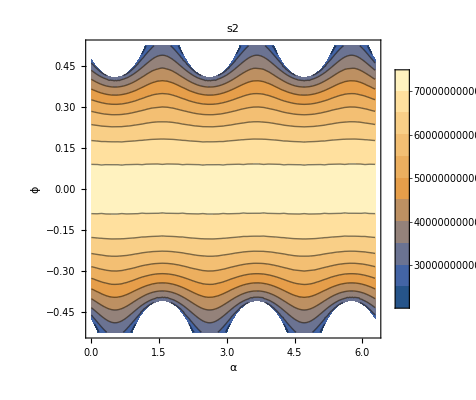

```mathematica
ContourPlot[solveS2[{lcr,lst,rb,ra}/.lendata,α,ϕ,600],{α,0,360*(π/180)},{ϕ,-30*(π/180),30*(π/180)},PlotLegends->Automatic,FrameLabel->{α,ϕ},PlotLabel->"s2"]
```